```mathematica
(*http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html*)
(*ResourceFunction["MaTeXInstall"][];*) (* <-Run  once forevere *) 
Needs["MaTeX`"]
Myfontsize=22;
myimsize=800;
texStyle={FontFamily->"CMU Serif",FontSize->Myfontsize};
SetOptions[Plot,Frame-> True,ImageSize->myimsize,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[LogLogPlot,Frame-> True,ImageSize->myimsize,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListPlot,Frame-> True,ImageSize->myimsize,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogPlot,Frame-> True,ImageSize->myimsize,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogLinearPlot,Frame-> True,ImageSize->myimsize,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogLogPlot,Frame-> True,ImageSize->myimsize,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListVectorPlot,Frame-> True,ImageSize->myimsize,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLinePlot,Frame-> True,ImageSize->myimsize,FrameStyle->Directive[Black],BaseStyle->texStyle];
```

```mathematica
toXY[listX_,listY_]:=Table[{listX[[i]],listY[[i]]},{i,1,Length[listX]}]
```

```mathematica
c=Import["/home/carlo/Desktop/test_EHL_direct_vs_iter/iterHMATT.csv","csv"];
sizeH=Table[c[[i]][[1]],{i,1,Length[c]}];
anderTimeH=Table[c[[i]][[2]],{i,1,Length[c]}];
anderTimeRelH=Table[100*anderTimeH[[i]]/c[[i]][[2]],{i,1,Length[c]}];

iterSolTimeH=Table[c[[i]][[2]]-c[[i]][[4]]-c[[i]][[3]],{i,1,Length[c]}];
iterSolTimeRelH=Table[100*iterSolTimeH[[i]]/c[[i]][[2]],{i,1,Length[c]}];
store=0.;
anderTimeCumH=Table[store=store+c[[i]][[2]],{i,1,Length[c]}];

aTimeH=Table[c[[i]][[3]],{i,1,Length[c]}];
aTimeRelH=Table[100*aTimeH[[i]]/c[[i]][[2]],{i,1,Length[c]}];

iLUTimeH=Table[c[[i]][[4]],{i,1,Length[c]}];
iLUTimeRelH=Table[100*iLUTimeH[[i]]/c[[i]][[2]],{i,1,Length[c]}];
iterSolH=Table[c[[i]][[5]],{i,1,Length[c]}];
iterAnderH=Table[c[[i]][[6]],{i,1,Length[c]}];
iterSolMeanH=Table[c[[i]][[5]]/c[[i]][[6]]//N,{i,1,Length[c]}];
```

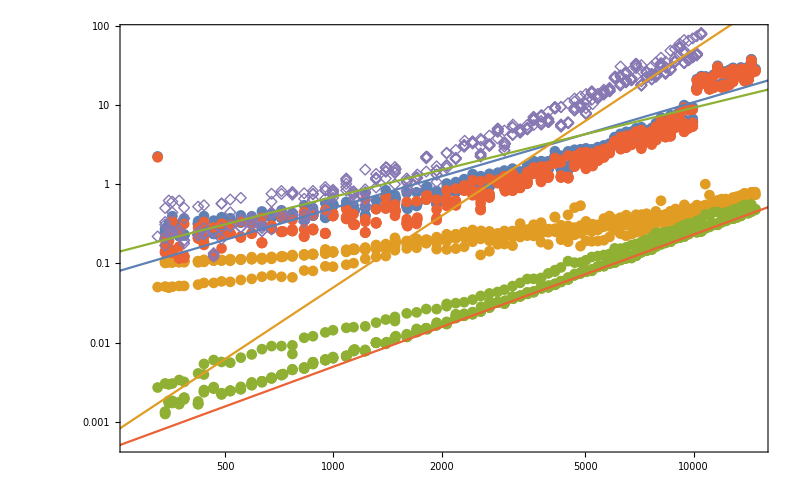

```mathematica
anderTimePH=toXY[sizeH,anderTimeH];
iterSolTimePH=toXY[sizeH,iterSolTimeH];
aTimePH=toXY[sizeH,aTimeH];
iLUTimePH=toXY[sizeH,iLUTimeH];
legend=PointLegend[{MaTeX["\\text{solve A(x).x=b(x) -ITERATIVE} ",FontSize->Myfontsize-2],
MaTeX["\\text{get ~A(x)} ",FontSize->Myfontsize-2],
MaTeX["\\text{get iLUT(~A(x))} ",FontSize->Myfontsize-2],
MaTeX["\\text{solve A.x=b} ",FontSize->Myfontsize-2],
MaTeX["\\text{solve A(x).x=b(x) -DIRECT} ",FontSize->Myfontsize-2]},LegendMarkerSize->20];
legend2={MaTeX["\\propto N^{4/3}",FontSize->Myfontsize-2],
MaTeX["\\propto N^{3}",FontSize->Myfontsize-2],
MaTeX["\\propto N \\text{Log}[N]",FontSize->Myfontsize-2],
MaTeX["\\propto N^{5/3}",FontSize->Myfontsize-2]};
xlabel=MaTeX["\\text{N = rank(A)} ",FontSize->Myfontsize-2];
ylabel=MaTeX["\\text{time [s]} ",FontSize->Myfontsize-2];
markersize=11;
Show[
ListLogLogPlot[{anderTimePH,aTimePH,iLUTimePH,iterSolTimePH,anderTimeDP},
PlotLegends->legend,
Frame->True,
PlotMarkers->{{"•",markersize},{"•",markersize},{"•",markersize},{"•",markersize},{"◇",markersize}},
FrameLabel->{xlabel,ylabel}],LogLogPlot[{0.00005 x^(4/3),0.00000000005 x^3,0.0001x Log[x],0.00000005 x^(5/3)},{x,10,30000},PlotLegends->legend2]]
```

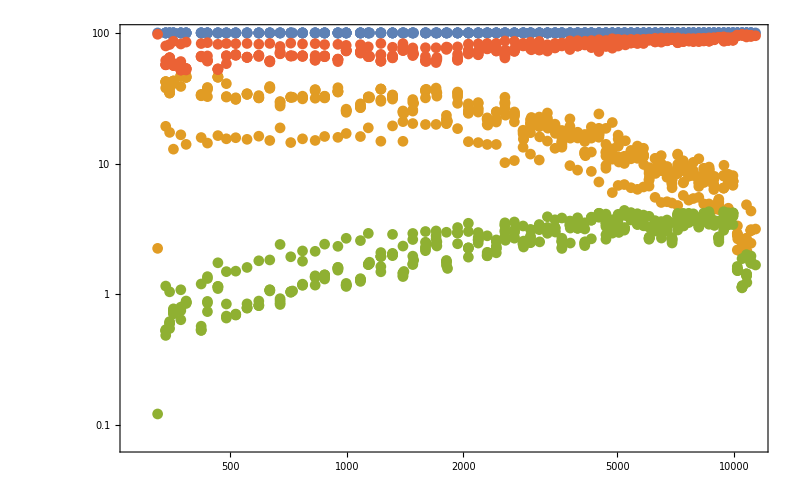

```mathematica
anderTimePRelH=toXY[sizeH,anderTimeRelH];
iterSolTimePRelH=toXY[sizeH,iterSolTimeRelH];
aTimePRelH=toXY[sizeH,aTimeRelH];
iLUTimePRelH=toXY[sizeH,iLUTimeRelH];
legend={MaTeX["\\text{solve A(x)} * \\text{x=b(x)} ",FontSize->Myfontsize-2],
MaTeX["\\text{get \\~A(x)} ",FontSize->Myfontsize-2],
MaTeX["\\text{get iLUT(\\~A(x))} ",FontSize->Myfontsize-2],
MaTeX["\\text{solve A.x=b} ",FontSize->Myfontsize-2]};
xlabel=MaTeX["\\text{N = rank(A)} ",FontSize->Myfontsize-2];
ylabel=Rotate[MaTeX["\\frac{\\text{ time}}{\\text{ time[ A(x)} * \\text{x=b(x) ]}} [\\%]",FontSize->Myfontsize-2],-Pi/2];
Show[
ListLogLogPlot[{anderTimePRelH,aTimePRelH,iLUTimePRelH,iterSolTimePRelH},
PlotLegends->legend,
Frame->True,
PlotMarkers->{{"•",markersize},{"•",markersize},{"•",markersize},{"•",markersize}},
FrameLabel->{xlabel,ylabel}]]
```

```mathematica
d= Import["/home/carlo/Desktop/test_EHL_direct_vs_iter/directT.csv","csv"];
sizeD=Table[d[[i]][[1]],{i,1,Length[d]}];
anderTimeD=Table[d[[i]][[2]],{i,1,Length[d]}];
anderTimeRelD=Table[100*anderTimeD[[i]]/d[[i]][[2]],{i,1,Length[d]}];
iterSolTimeD=Table[d[[i]][[2]]-d[[i]][[3]],{i,1,Length[d]}];
iterSolTimeRelD=Table[100*iterSolTimeD[[i]]/d[[i]][[2]],{i,1,Length[d]}];
store=0.;
anderTimeCumDP=Table[store=store+d[[i]][[2]];{d[[i]][[1]],store/60},{i,1,Length[d]}];

aTimeD=Table[d[[i]][[3]],{i,1,Length[d]}];
aTimeRelD=Table[100*aTimeD[[i]]/d[[i]][[2]],{i,1,Length[d]}];
iterAnderD=Table[d[[i]][[4]],{i,1,Length[d]}];

anderTimeDP=toXY[sizeD,anderTimeD];
iterSolTimeDP=toXY[sizeD,iterSolTimeD];
aTimeDP=toXY[sizeD,aTimeD];
```

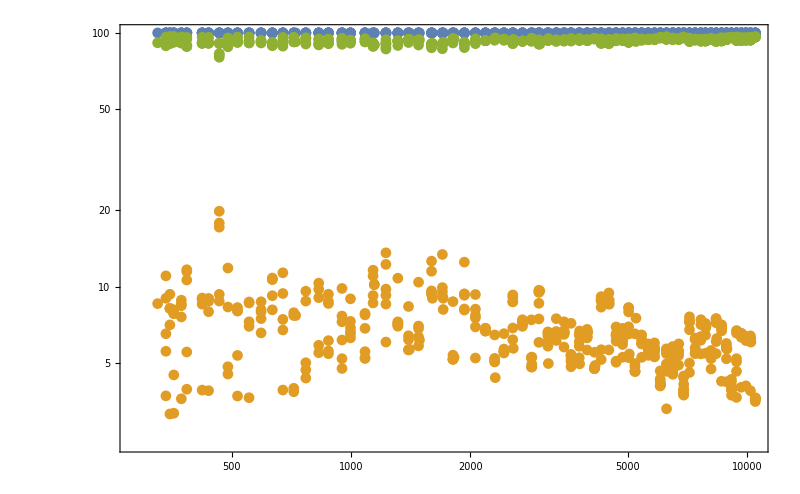

```mathematica
anderTimePRelD=toXY[sizeD,anderTimeRelD];
iterSolTimePRelD=toXY[sizeD,iterSolTimeRelD];
aTimePRelD=toXY[sizeD,aTimeRelD];
legend={MaTeX["\\text{solve A(x)} * \\text{x=b(x)} ",FontSize->Myfontsize-2],
MaTeX["\\text{get \\~A(x)} ",FontSize->Myfontsize-2],
MaTeX["\\text{solve A.x=b} ",FontSize->Myfontsize-2]};
xlabel=MaTeX["\\text{N = rank(A)} ",FontSize->Myfontsize-2];
ylabel=Rotate[MaTeX["\\frac{\\text{ time}}{\\text{ time[ A(x)} * \\text{x=b(x) ]}} [\\%]",FontSize->Myfontsize-2],-Pi/2];
Show[
ListLogLogPlot[{anderTimePRelD,aTimePRelD,iterSolTimePRelD},
PlotLegends->legend,
Frame->True,
PlotMarkers->{{"•",markersize},{"•",markersize},{"•",markersize},{"•",markersize}},
FrameLabel->{xlabel,ylabel}]]
```

```mathematica
a = Import["/home/carlo/Desktop/test_EHL_direct_vs_iter/iterT.csv","csv"];
size=Table[a[[i]][[1]],{i,1,Length[a]}];
anderTime=Table[a[[i]][[2]],{i,1,Length[a]}];
anderTimeRel=Table[100*anderTime[[i]]/a[[i]][[2]],{i,1,Length[a]}];

iterSolTime=Table[a[[i]][[2]]-a[[i]][[4]]-a[[i]][[3]],{i,1,Length[a]}];
iterSolTimeRel=Table[100*iterSolTime[[i]]/a[[i]][[2]],{i,1,Length[a]}];
store=0.;
anderTimeCum=Table[store=store+a[[i]][[2]],{i,1,Length[a]}];

aTime=Table[a[[i]][[3]],{i,1,Length[a]}];
aTimeRel=Table[100*aTime[[i]]/a[[i]][[2]],{i,1,Length[a]}];

iLUTime=Table[a[[i]][[4]],{i,1,Length[a]}];
iLUTimeRel=Table[100*iLUTime[[i]]/a[[i]][[2]],{i,1,Length[a]}];
iterSol=Table[a[[i]][[5]],{i,1,Length[a]}];
iterAnder=Table[a[[i]][[6]],{i,1,Length[a]}];
iterSolMean=Table[a[[i]][[5]]/a[[i]][[6]]//N,{i,1,Length[a]}];
toXY[listX_,listY_]:=Table[{listX[[i]],listY[[i]]},{i,1,Length[listX]}]
```

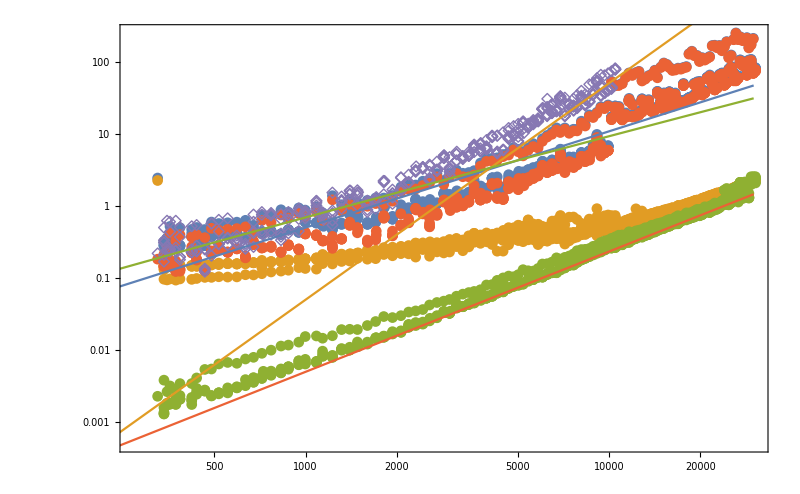

```mathematica
anderTimeP=toXY[size,anderTime];
iterSolTimeP=toXY[size,iterSolTime];
aTimeP=toXY[size,aTime];
iLUTimeP=toXY[size,iLUTime];
legend=PointLegend[{MaTeX["\\text{solve A(x).x=b(x) -ITERATIVE} ",FontSize->Myfontsize-2],
MaTeX["\\text{get ~A(x)} ",FontSize->Myfontsize-2],
MaTeX["\\text{get iLUT(~A(x))} ",FontSize->Myfontsize-2],
MaTeX["\\text{solve A.x=b} ",FontSize->Myfontsize-2],
MaTeX["\\text{solve A(x).x=b(x) -DIRECT} ",FontSize->Myfontsize-2]},LegendMarkerSize->20];
legend2={MaTeX["\\propto N^{4/3}",FontSize->Myfontsize-2],
MaTeX["\\propto N^{3}",FontSize->Myfontsize-2],
MaTeX["\\propto N \\text{Log}[N]",FontSize->Myfontsize-2],
MaTeX["\\propto N^{5/3}",FontSize->Myfontsize-2]};
xlabel=MaTeX["\\text{N = rank(A)} ",FontSize->Myfontsize-2];
ylabel=MaTeX["\\text{time [s]} ",FontSize->Myfontsize-2];
markersize=11;
Show[
ListLogLogPlot[{anderTimeP,aTimeP,iLUTimeP,iterSolTimeP,anderTimeDP},
PlotLegends->legend,
Frame->True,
PlotMarkers->{{"•",markersize},{"•",markersize},{"•",markersize},{"•",markersize},{"◇",markersize}},
FrameLabel->{xlabel,ylabel}],LogLogPlot[{0.00005 x^(4/3),0.00000000005 x^3,0.0001x Log[x],0.00000005 x^(5/3)},{x,10,30000},PlotLegends->legend2]]
```

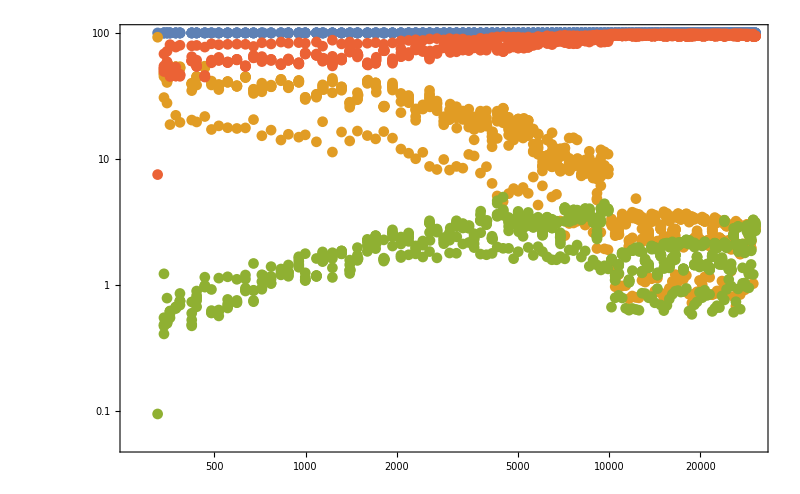

```mathematica
anderTimePRel=toXY[size,anderTimeRel];
iterSolTimePRel=toXY[size,iterSolTimeRel];
aTimePRel=toXY[size,aTimeRel];
iLUTimePRel=toXY[size,iLUTimeRel];
legend={MaTeX["\\text{solve A(x)} * \\text{x=b(x)} ",FontSize->Myfontsize-2],
MaTeX["\\text{get \\~A(x)} ",FontSize->Myfontsize-2],
MaTeX["\\text{get iLUT(\\~A(x))} ",FontSize->Myfontsize-2],
MaTeX["\\text{solve A.x=b} ",FontSize->Myfontsize-2]};
xlabel=MaTeX["\\text{N = rank(A)} ",FontSize->Myfontsize-2];
ylabel=Rotate[MaTeX["\\frac{\\text{ time}}{\\text{ time[ A(x)} * \\text{x=b(x) ]}} [\\%]",FontSize->Myfontsize-2],-Pi/2];
Show[
ListLogLogPlot[{anderTimePRel,aTimePRel,iLUTimePRel,iterSolTimePRel},
PlotLegends->legend,
Frame->True,
PlotMarkers->{{"•",markersize},{"•",markersize},{"•",markersize},{"•",markersize}},
FrameLabel->{xlabel,ylabel}]]
```

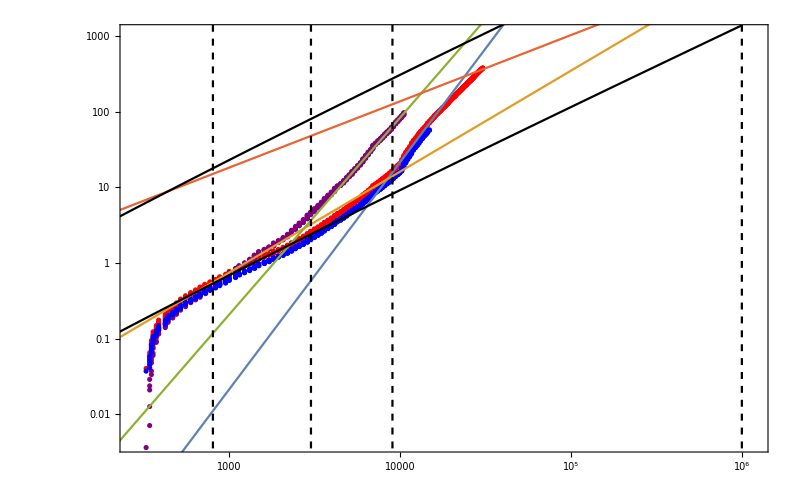

```mathematica
anderTimeCumP=toXY[size,anderTimeCum/60];
anderTimeCumPH=toXY[sizeH,anderTimeCumH/60];
legend={MaTeX["\\text{iterative - OpenMP (shared memory)} ",FontSize->Myfontsize-2],
MaTeX["\\text{direct} ",FontSize->Myfontsize-2],
MaTeX["\\text{iterative - HMAT} ",FontSize->Myfontsize-2]};
legend2={
MaTeX["\\propto N^{3}",FontSize->Myfontsize-2],
MaTeX["\\propto N^{4/3}",FontSize->Myfontsize-2],
MaTeX["\\propto N^{26/10}",FontSize->Myfontsize-2],
MaTeX["\\propto N^{21/24}",FontSize->Myfontsize-2]};
xlabel=MaTeX["\\text{N = rank(A)} ",FontSize->Myfontsize-2];
legend3={MaTeX["\\propto N \\text{Log}[N]",FontSize->Myfontsize-2]};
xlabel=MaTeX["\\text{N = rank(A)} ",FontSize->Myfontsize-2];
ylabel=Rotate[MaTeX["\\substack{\\text{cumul. time [min]} \\\\ {\\text{to solve A(x)} * \\text{x=b(x)}} } ",FontSize->Myfontsize],-Pi/2];
Show[
ListLogLogPlot[{anderTimeCumP,anderTimeCumDP,anderTimeCumPH},
PlotLegends->legend,
Frame->True,
FrameLabel->{xlabel,ylabel},
PlotStyle->{Red,Purple,Blue}],
LogLogPlot[{0.0000000013 x^3/60,0.0045 x^(4/3)/60,0.0000002 x^(260/100)/60,2.6 x^(21/24)/60},{x,10,1000000},PlotLegends->legend2],
LogLogPlot[{0.006x Log[x]/60,0.2x Log[x]/60},{x,10,1000000},PlotLegends->legend3,PlotStyle->Black],
ListLogLogPlot[{{800,0.001},{800,10000}},Joined->True,PlotStyle->{Dashed,Black,Thin}],
ListLogLogPlot[{{1000000,0.001},{1000000,10000}},Joined->True,PlotStyle->{Dashed,Black,Thin}],
ListLogLogPlot[{{3000,0.001},{3000,10000}},Joined->True,PlotStyle->{Dashed,Black,Thin}],
ListLogLogPlot[{{9000,0.001},{9000,10000}},Joined->True,PlotStyle->{Dashed,Black,Thin}],PlotRange->{{5.6,14},{-5.5,7}}]
```

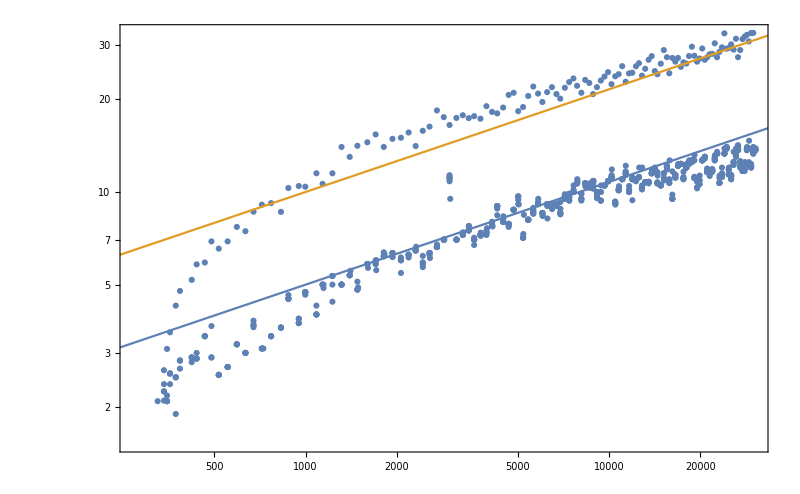

```mathematica
iterSolMeanP=toXY[size,iterSolMean];
xlabel=MaTeX["\\text{N = rank(A)} ",FontSize->Myfontsize-2];
ylabel=Rotate[MaTeX["<\\text{  iter }>{\\text{for A} * \\text{x=b}} ",FontSize->Myfontsize-2],-Pi/2];
legend={"<N iter> for A.x=b"};legend={MaTeX["<\\text{  iter }>{\\text{for A} * \\text{x=b}} ",FontSize->Myfontsize-2]};
legend2={MaTeX["\\frac{1}{2}\\, N^{1/3}",FontSize->Myfontsize-2],
MaTeX["N^{1/3}",FontSize->Myfontsize-2]};
Show[ListLogLogPlot[iterSolMeanP,PlotLegends->legend,
Frame->True,
FrameLabel->{xlabel,ylabel}],LogLogPlot[{0.5 x^(1/3),1. x^(1/3)},{x,10,40000},PlotLegends->legend2]]
```

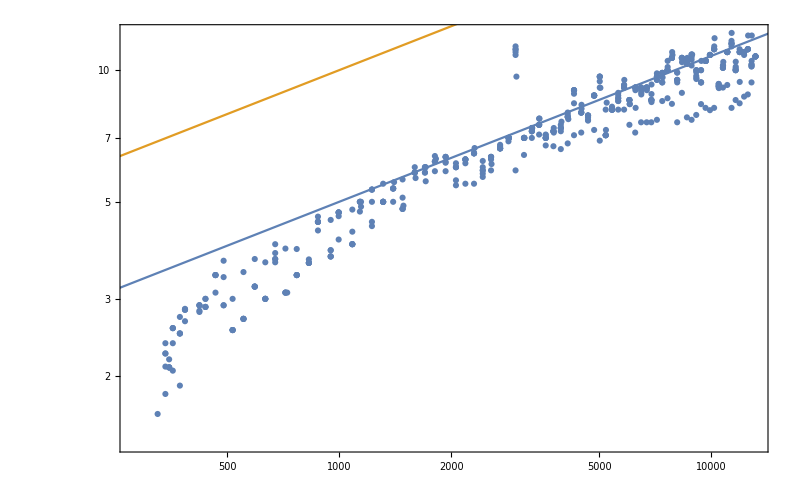

```mathematica
iterSolMeanPH=toXY[sizeH,iterSolMeanH];
xlabel=MaTeX["\\text{N = rank(A)} ",FontSize->Myfontsize-2];
ylabel=Rotate[MaTeX["<\\text{  iter }>{\\text{for A} * \\text{x=b}} ",FontSize->Myfontsize-2],-Pi/2];
legend={"<N iter> for A.x=b"};legend={MaTeX["<\\text{  iter }>{\\text{for A} * \\text{x=b}} ",FontSize->Myfontsize-2]};
legend2={MaTeX["\\frac{1}{2}\\, N^{1/3}",FontSize->Myfontsize-2],
MaTeX["N^{1/3}",FontSize->Myfontsize-2]};
Show[ListLogLogPlot[iterSolMeanPH,PlotLegends->legend,
Frame->True,
FrameLabel->{xlabel,ylabel}],LogLogPlot[{0.5 x^(1/3),1. x^(1/3)},{x,10,40000},PlotLegends->legend2]]
```

```mathematica
(2*20)/(2*10/(121-1))+1//N
```

241.